#### String Manipulation Function

```mathematica
ModStrx[x_,n_]:=StringReplace[StringReplace[ToString[x,FortranForm],{ToString[N[ⅇ,n],FortranForm]->"E",ToString[N[π,n],FortranForm]->"pi",ToString[N[1/π,n],FortranForm]->"1/pi"}],{"E**"->"exp","**"->"^","Sqrt"->"sqrt","Sech"->"sech","Tanh"->"tanh","Log"->"log"}]
```

```mathematica
ModStrxNN[x_]:=StringReplace[ToString[x,FortranForm],{"E**"->"exp","**"->"^","Sqrt"->"sqrt","Sech"->"sech","Tanh"->"tanh","Log"->"log"}]
```

```mathematica
GreekName[x_]:=StringReplace[x,{"α"->"alpha","β"->"beta","γ"->"gamma","δ"->"delta","ϵ"->"epsilon","θ"->"theta","ϕ"->"phi","κ"->"kappa","λ"->"lambda"}]
```

#### Reference Potential Function

U_(ref,n) from [Safari, 2011, JEM]:

```mathematica
Urefn[θ_]:=a1+a2 Exp[a3 θ]+a4 Tanh[(θ+a5)/a6]+a7 Tanh[(θ+a8)/a9]+a10 Tanh[(θ+a11)/a12]+a13 Tanh[(θ+a14)/a15]/.{a1->0.6379,a2->0.5416,a3->-305.5309,a4->0.044,a5->-0.1958,a6->-0.1088,a7->-0.1978,a8->-1.0571,a9->0.0854,a10->-0.6875,a11->0.0117,a12->0.0529,a13->-0.0175,a14->-0.5692,a15->0.0875}
```

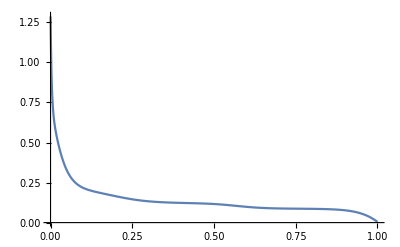

```mathematica
Plot[Urefn[θ],{θ,0,1},PlotRange->All]
```

Take derivative of U_(ref,n):

```mathematica
DUrefn[θ_]=D[Urefn[θ],θ]
```

-165.476 ⅇ^(-305.531 θ)-2.31616 Sech[11.7096 (-1.0571+θ)]^2-0.2 Sech[11.4286 (-0.5692+θ)]^2-0.404412 Sech[9.19118 (-0.1958+θ)]^2-12.9962 Sech[18.9036 (0.0117+θ)]^2

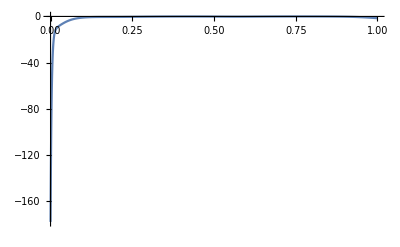

```mathematica
Plot[DUrefn[θ],{θ,0,1},PlotRange->All]
```

U_(ref,p) from [Safari, 2011, JEM]:

```mathematica
Urefp[θ_]:=c1+c2 Exp[c3 (1-θ)^c4]+c5 Exp[c6(1-θ)^c7]+c8 Exp[c9 (1-θ)^c10]/.{c1->3.4323,c2->-0.8428,c3->-80.2493,c4->1.3198,c5->-3.2474×10^-6,c6->20.2645,c7->3.8003,c8->3.2482×10^-6,c9->20.2646,c10->3.7995}
```

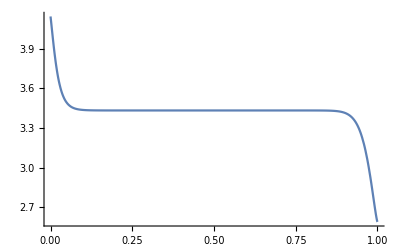

```mathematica
Plot[Urefp[θ],{θ,0,1},PlotRange->All]
```

Take derivative of U_(ref,p):

```mathematica
DUrefp[θ_]=D[Urefp[θ],θ]
```

-89.2635 ⅇ^(-80.2493 (1-θ)^1.3198) (1-θ)^0.3198-0.000250096 ⅇ^(20.2646 (1-θ)^3.7995) (1-θ)^2.7995+0.000250086 ⅇ^(20.2645 (1-θ)^3.8003) (1-θ)^2.8003

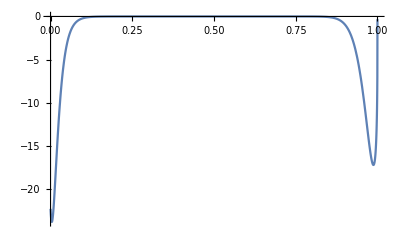

```mathematica
Plot[DUrefp[θ],{θ,0,1},PlotRange->All]
```

#### String Manipulation of the Derivatives

```mathematica
MDn=ModStrxNN[DUrefn[θ]]
```

-165.47553544/exp(305.5309*θ) - 2.31615925058548*sech(11.709601873536299*(-1.0571 + θ))^2 - 0.2*sech(11.428571428571429*(-0.5692 + θ))^2 - 0.40441176470588236*sech(9.191176470588236*(-0.1958 + θ))^2 - 12.996219281663516*sech(18.90359168241966*(0.0117 + θ))^2

```mathematica
MDp=ModStrxNN[DUrefp[θ]]
```

(-89.26349843079201*(1 - θ)^0.3198000000000001)/exp(80.2493*(1 - θ)^1.3198) - 0.00025009628839914*exp(20.2646*(1 - θ)^3.7995)*(1 - θ)^2.7995 + 0.00025008610382119*exp(20.2645*(1 - θ)^3.8003)*(1 - θ)^2.8003

```mathematica
GreekName[MDn]
```

-165.47553544/exp(305.5309*theta) - 2.31615925058548*sech(11.709601873536299*(-1.0571 + theta))^2 - 0.2*sech(11.428571428571429*(-0.5692 + theta))^2 - 0.40441176470588236*sech(9.191176470588236*(-0.1958 + theta))^2 - 12.996219281663516*sech(18.90359168241966*(0.0117 + theta))^2

```mathematica
GreekName[MDp]
```

(-89.26349843079201*(1 - theta)^0.3198000000000001)/exp(80.2493*(1 - theta)^1.3198) - 0.00025009628839914*exp(20.2646*(1 - theta)^3.7995)*(1 - theta)^2.7995 + 0.00025008610382119*exp(20.2645*(1 - theta)^3.8003)*(1 - theta)^2.8003